```mathematica
σS=0.8;
σF=0.3;
dt=1.0/365.25;
f=50.0;
```

```mathematica
pv[T_Real,n_Real,k_Real]:=FinancialDerivative[{"Future","European","Call"},{"StrikePrice"->k,"Expiration"->T},{"CurrentPrice"->f,"Volatility"->√((σF^2 T+σS^2 n dt)/(T+n dt)),"InterestRate"->0}]
```

```mathematica
pvall[T_Real,k_Real]:=Mean[Table[FinancialDerivative[{"Future","European","Call"},{"StrikePrice"->k,"Expiration"->T},{"CurrentPrice"->f,"Volatility"->√((σF^2 T+σS^2 i dt)/(T+i dt)),"InterestRate"->0}],{i,0,29}]]
```

```mathematica
diff[T_Real,n_Real,k_Real]:=pvall[T,k]-pv[T,n,k]
```

```mathematica
implVol[T_Real,n_Real,k_Real]:=With[{σ=FinancialDerivative[{"Future","European","Call"},{"StrikePrice"->k,"Expiration"->T,"Value"->pvall[T,k]},{"CurrentPrice"->f,"InterestRate"->0},"ImpliedVolatility"]},√((σ^2(T+n dt)-σF^2 T)/(n dt))]
```

### Exact n

```mathematica
resATM=ParallelTable[{it 30/365.25,FindRoot[diff[it 30/365.25,x,f]==0,{x,5}]_[[1,2]]},{it,1,36}];
```

```mathematica
resOTM=ParallelTable[{it 30/365.25,FindRoot[diff[it 30/365.25,x,1.2f]==0,{x,5}]_[[1,2]]},{it,1,36}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
resITM=ParallelTable[{it 30/365.25,FindRoot[diff[it 30/365.25,x,0.8f]==0,{x,5}]_[[1,2]]},{it,1,36}];
```

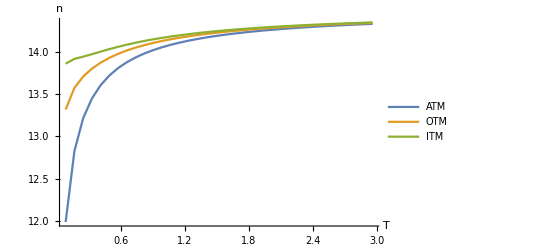

```mathematica
ListPlot[{resATM,resOTM,resITM},Joined->True,PlotRange->All,AxesLabel->{"T","n"},PlotLegends->{"ATM","OTM","ITM"}]
```

### Using long term n

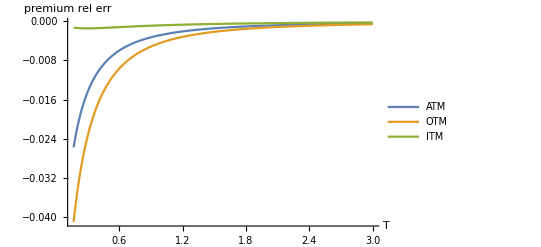

```mathematica
Plot[{diff[x,14.5,f]/pv[x,14.5,f],diff[x,14.5,1.2f]/pv[x,14.5,1.2f],diff[x,14.5,0.8f]/pv[x,14.5,0.8f]},{x,1.0/6,3},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"T","premium rel err"},PlotLegends->{"ATM","OTM","ITM"}]
```

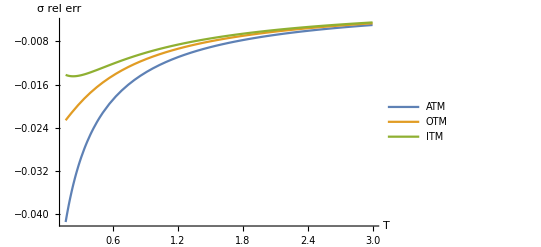

```mathematica
Plot[{(implVol[x,14.5,f]-σS)/σS,(implVol[x,14.5,1.2f]-σS)/σS,(implVol[x,14.5,0.8f]-σS)/σS},{x,1.0/6,3},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"T","σ rel err"},PlotLegends->{"ATM","OTM","ITM"}]
```

### Optimal n?

```mathematica
nn=13.9
```

13.9

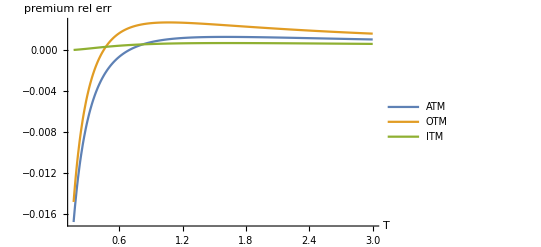

```mathematica
Plot[{diff[x,nn,f]/pv[x,nn,f],diff[x,nn,1.2f]/pv[x,nn,1.2f],diff[x,nn,0.8f]/pv[x,nn,0.8f]},{x,1.0/6,3},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"T","premium rel err"},PlotLegends->{"ATM","OTM","ITM"}]
```

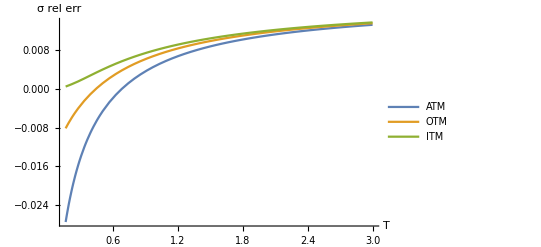

```mathematica
Plot[{(implVol[x,nn,f]-σS)/σS,(implVol[x,nn,1.2f]-σS)/σS,(implVol[x,nn,0.8f]-σS)/σS},{x,1.0/6,3},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"T","σ rel err"},PlotLegends->{"ATM","OTM","ITM"}]
```

### Functional n

```mathematica
nfunc=Interpolation[{resATM_[[All,1]],0.5(resATM_[[All,2]]+resOTM_[[All,2]])}ᵀ];
```

```mathematica
nfunc=Interpolation[resOTM];
```

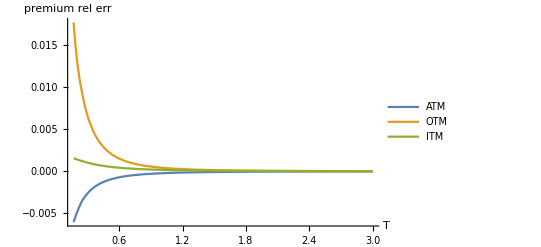

```mathematica
Plot[{diff[x,nfunc[x],f]/pv[x,nfunc[x],f],diff[x,nfunc[x],1.2f]/pv[x,nfunc[x],1.2f],diff[x,nfunc[x],0.8f]/pv[x,nfunc[x],0.8f]},{x,1.0/6,3},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"T","premium rel err"},PlotLegends->{"ATM","OTM","ITM"}]
```

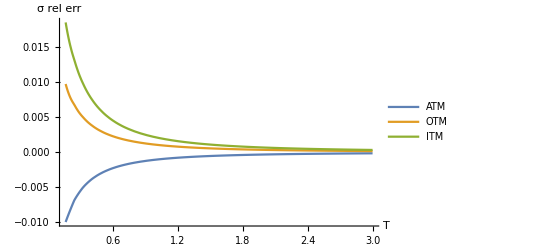

```mathematica
Plot[{(implVol[x,nfunc[x],f]-σS)/σS,(implVol[x,nfunc[x],1.2f]-σS)/σS,(implVol[x,nfunc[x],0.8f]-σS)/σS},{x,1.0/6,3},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"T","σ rel err"},PlotLegends->{"ATM","OTM","ITM"}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

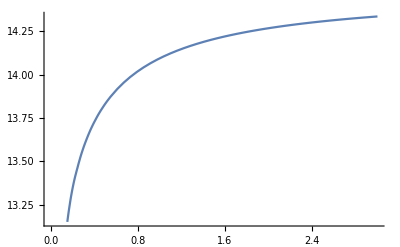

```mathematica
Plot[nfunc[x],{x,0,3}]
```